# Generating Figures 2 and 3 in the article “Obscuring digital route choice information prevents delay-induced congestion”

## Figure 2: Routing in a two-route network with delayed information

Solving the delay-differential equations by numerical integration

With this notebook, we solve the delayed differential equations of vehicle numbers on two streets numerically by integration, plot some resulting street load dynamics and find whether congestion arises for given sets of parameters.

To start, we first define our travel time, the corresponding in-rates and the differential equations for the two streets A and C.

```mathematica
Quit[]
```

```mathematica
(*Parameter set*)
N0V=1;
βV=1;
t0A=1;
t0C=1;
```

```mathematica
(*Travel times*)
```

```mathematica
tA[t0A_, N0_,NA_]:=t0A*(Exp[NA/N0]-1)/(NA/N0);
tC[t0C_,N0_,NC_]:=t0C*(Exp[NC/N0]-1)/(NC/N0);
```

```mathematica
(*In-rates*)
rINA[β_,N0_, t0A_, t0C_, NA_, NC_]:=1/(1+Exp[β*(tA[t0A,N0,NA]-tC[t0C,N0,NC])]);
rINC[β_, N0_, t0A_, t0C_, NA_, NC_]:=1/(1+Exp[-β*(tA[t0A,N0,NA]-tC[t0C,N0,NC])]);
```

```mathematica
(*Delay-differential equations*)
NAEqns[νIN_, NAinit_, t_, τ_]:={D[NA[t],t]==νIN*(rINA[βV, N0V, t0A, t0C, NA[t-τ], NC[t-τ]])-((NA[t]^2)/(t0A*N0V))/(Exp[NA[t]/N0V]-1), NA[t/;t≤0]==NAinit};
NCEqns[νIN_, NCinit_, t_, τ_]:={D[NC[t],t]== νIN *(rINC[βV, N0V, t0A, t0C, NA[t-τ], NC[t-τ]])-((NC[t]^2)/(t0C*N0V))/(Exp[NC[t]/N0V]-1), NC[t/;t≤0]==NCinit};
```

Our differential equation has two fixed points, which we find by determining the root of the equation’s right-hand side.

```mathematica
(*Right-hand side of the differential equation for one street*)
DGLN1τ[ν_,N1_,N2_,N1τ_,N2τ_,N0_]:=(ν/(1+Exp[tA[1,N0,N1τ]-tC[1,N0,N2τ]]))-(N1^2)/(N0*(Exp[N1/N0]-1));
(*Function which gives the stable fixed point for given in-rate and effective capacity*)
findFixedPoint[N00_,ν0_]:=Min[Table[FindRoot[DGLN1τ[ν0,Nx,Nx,Nx,Nx,N00]==0,{Nx,x0}][[1,2]],{x0,0.01,2}]]
```

Now we have all the tools to integrate the differential equations numerically for given parameters.

```mathematica
(*Function to determine the solution of the delay differential equations numerically*)
SolsDDE[νIN_, NAinit_, NCinit_, t_, τ_, tfin_]:={NDSolve[Flatten[{NAEqns[νIN, NAinit, t, τ], NCEqns[νIN, NCinit, t, τ], {WhenEvent[(NA[t]+NC[t])==100, {Set[t0,t], "StopIntegration"}], WhenEvent[t==tfin-1, Set[t0,tfin]]}}], {NA[t], NC[t]}, {t, 0,tfin}][[1]], t0};
```

In Figs. 2b-d of the article, we show the numerical DDE solutions for three different delays and a fixed in-rate.

```mathematica
(*Calculate the stable fixed for the given in-rate*)
νIn0=1.1;
τ1=0;
τ2=4;
τ3=8;
fp=findFixedPoint[1,νIn0];
Sol1=SolsDDE[νIn0, fp+0.1, fp-0.1, t,τ1,500];
Sol2=SolsDDE[νIn0, fp+0.1, fp-0.1, t,τ2,500];
Sol3=SolsDDE[νIn0, fp+0.1, fp-0.1, t,τ3,500];
```

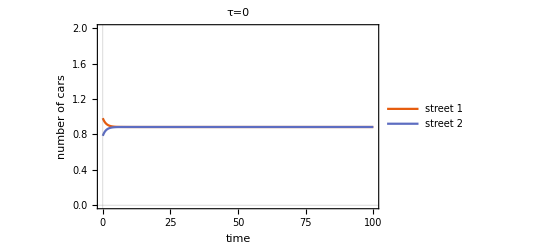

```mathematica
Plot[{NA[t]/.Sol1[[1]], NC[t]/.Sol1[[1]]}, {t, 0, 100},
 PlotRange->{{0,100}, {0,2}}, PlotTheme->"Scientific", FrameLabel->{"time", "number of cars"}, PlotLegends->{"street 1", "street 2"}, PlotLabel-> "τ=0"]
```

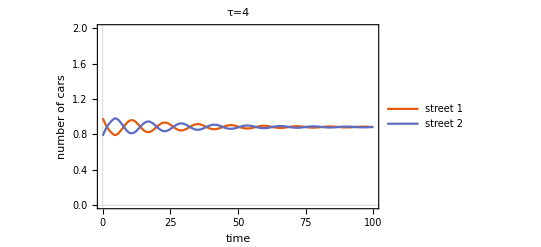

```mathematica
Plot[{NA[t]/.Sol2[[1]], NC[t]/.Sol2[[1]]}, {t, 0, 100}, 
 PlotRange->{{0,100}, {0,2}}, PlotTheme->"Scientific", FrameLabel->{"time", "number of cars"}, PlotLegends->{"street 1", "street 2"}, PlotLabel-> "τ=4"]
```

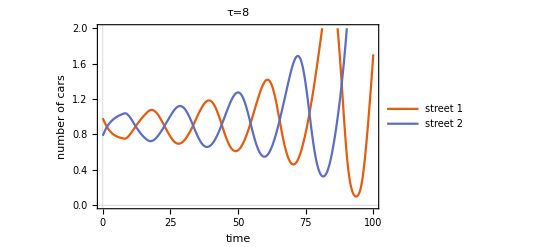

```mathematica
Plot[{NA[t]/.Sol3[[1]], NC[t]/.Sol3[[1]]}, {t, 0, 100}, 
 PlotRange->{{0,100}, {0,2}}, PlotTheme->"Scientific", FrameLabel->{"time", "number of cars"}, PlotLegends->{"street 1", "street 2"}, PlotLabel-> "τ=8"]
```

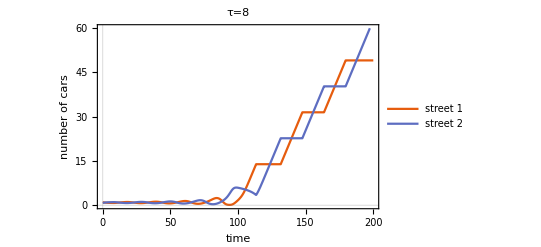

```mathematica
Plot[{NA[t]/.Sol3[[1]], NC[t]/.Sol3[[1]]}, {t, 0, 200}, 
 PlotRange->{{0,200}, {0,60}}, PlotTheme->"Scientific", FrameLabel->{"time", "number of cars"}, PlotLegends->{"street 1", "street 2"} , PlotLabel-> "τ=8"]
```

In addition to these exemplary dynamics, we want to determine for which pairs of in-rate and delay congestion occurs. To this end, we define a function which for each DDE solution finds whether the overall number of vehicles on the streets continuously rises or not.
We save the results for the considered range of delays and in-rates as a csv-file to then plot the phase diagram with python (see the jupyter notebook and respective modules for details).

```mathematica
(*Determine maximal values of DDE solutions for small and large time values; then build the difference of these two maxima. If the difference is ≤0, the solution is stable. Else, it is unstable.*)
MaxDiff[νIN_, t_, τ_, tfin_,df_]:=Module[
{fp,LastTime, FirstMax, SecondMax},
If[νIN≥1.3,fp=1.5, fp=findFixedPoint[N0V,νIN]];
LastTime=SolsDDE[νIN,fp+df, fp-df, t, τ, tfin][[2]]-2;
FirstMax=FindMaxValue[{(NA[t]+NC[t])/.Evaluate[SolsDDE[νIN,fp+df, fp-df, t, τ, LastTime]][[1]], t≥20 && t≤40}, t];
SecondMax=FindMaxValue[{(NA[t]+NC[t])/.Evaluate[SolsDDE[νIN,fp+df, fp-df, t, τ, LastTime]][[1]], t≥LastTime-20 && t<LastTime-1}, t];
Return[SecondMax-FirstMax]]
```

```mathematica
t0=500;
StabTable=Table[MaxDiff[νIN,  t, τ, 500, 0.1], {νIN, 1.0,1.31,0.01}, {τ, 0,20,0.5}];
Export["MaxDiffs_N0_10_nuMin_1_0_nuMax_1_31_dNu_0_01_tauMin_0_tauMax_20_dtau_0_5_Ninit_fp_pm_0_1_tMax_500.csv", StabTable]
```

Linear stability analysis of the DDE

In addition to the numerical integration of the DDE, we also determine the critical in-rates using linear stability analysis. Details on the theory behind this ansatz can be found in the article’s Appendix. 

The general idea is to linearize the differential equation around its stable fixed point and then for each delay find a critical in-rate with an eigenvalue with zero real part.

So again, we formulate our differential equations and from them derive two Jacobians.

```mathematica
Quit[]
```

```mathematica
(*Travel times*)
t1[ N0_,N1_]:=(Exp[N1/N0]-1)/(N1/N0);
t2[N0_,N2_]:=(Exp[N2/N0]-1)/(N2/N0);
```

```mathematica
(*Differential equations*)
DGLN1τ[ν_, N1_, N2_, N1τ_, N2τ_, N0_]:=(ν/(1+Exp[t1[N0, N1τ]-t2[N0, N2τ]]))-(N1^2)/(N0*(Exp[N1/N0]-1));
DGLN2τ[ν_, N1_, N2_,N1τ_, N2τ_, N0_]:=(ν/(1+Exp[t2[N0, N2τ]-t1[N0, N1τ]]))-(N2^2)/(N0*(Exp[N2/N0]-1));
```

```mathematica
(*Jacobi matrices*)
J011r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N1];
J012r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N2];
J021r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N1];
J022r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N2];
```

```mathematica
Jτ11r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N1τ];
Jτ12r=D[DGLN1τ[ν, N1, N2, N1τ, N2τ, N0], N2τ];
Jτ21r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N1τ];
Jτ22r=D[DGLN2τ[ν, N1, N2, N1τ, N2τ, N0], N2τ];
```

```mathematica
(*Stable fixed point*)
findFixedPoint[N00_,ν0_]:=Min[Table[FindRoot[DGLN1τ[ν0, Nx, Nx, Nx, Nx, N00]==0, {Nx,x0}][[1,2]],{x0,0.1,1.5}]]
```

```mathematica
(*Characteristic equation*)
form1[λ_, τ_,N00_,ν0_,fp_]:=(J011r+Exp[-λ*τ]Jτ11r-λ)*(J022r+Exp[-λ*τ]*Jτ22r-λ)-(J021r+Exp[-λ*τ]*Jτ21r)*(J012r+Exp[-λ*τ]*Jτ12r)/.N0->N00/.ν->ν0/.N1->fp/.N2->fp/.N1τ->fp/.N2τ->fp;
```

```mathematica
(*Initial conditions {Re,Im} for the root search*)
testRegion={Range[-1,1,0.2],Range[-1,1,0.2]};

findMaxReEigenvalue[N00_,ν0_,τ_,testRegion_List]:=Block[
{fp=findFixedPoint[N00,ν0]},
If[fp≥1.3,Return[1];];
Max[Re/@Flatten[Table[FindRoot[form1[λ,τ,N00, ν0,fp],{λ,x+RandomReal[{-0.01,0.01}]+y*I+RandomReal[{-0.01,0.01}]*I}][[1,2]],{x,testRegion[[1]]},{y,testRegion[[2]]}]]]
]
```

```mathematica
(*Interval halving to find the stability boundary for a given delay τ*)
findStabilityBoundaryFixedDelay[N00_,τ_]:=
Module[{minInRate=0.9,maxInRate=1.4,minReEv,maxReEv,midReEv},

minReEv=findMaxReEigenvalue[N00, minInRate, τ,testRegion];
maxReEv=findMaxReEigenvalue[N00, maxInRate, τ,testRegion];

While[(maxInRate-minInRate)>0.001,
If[minReEv<0∧maxReEv>0,
midReEv=findMaxReEigenvalue[N00, (minInRate+maxInRate)/2, τ,testRegion];
If[midReEv<0,minInRate=(minInRate+maxInRate)/2;minReEv=midReEv;,maxInRate=(minInRate+maxInRate)/2;maxReEv=midReEv;],
Break[];
];
];

If[(maxInRate-minInRate)≤0.001,
Return[{(minInRate+maxInRate)/2,True}];,
Return[{maxInRate,False}];
];
]
```

```mathematica
stabilityBoundaryfixedDelay=Table[{τ,findStabilityBoundaryFixedDelay[1,τ]},{τ,0,20,1}];
```

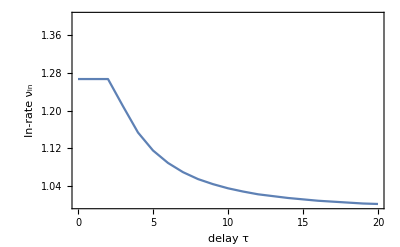

```mathematica
ListLinePlot[{#[[1]],If[#[[2,2]],#[[2,1]],∞]}&/@stabilityBoundaryfixedDelay,PlotRange->{{0,20},{1.0,1.4}},Frame->True,FrameLabel->{"delay τ","In-rate ν_in"}]
```

```mathematica
nuVals=Table[stabilityBoundaryfixedDelay[[n]][[2]][[1]], {n, 1,21,1}];
tauVals=Table[stabilityBoundaryfixedDelay[[n]][[1]], {n, 1,21,1}];
Export["stabBoundary_tauVals_N0_1.csv",tauVals];
Export["stabBoundary_nuVals_N0_1.csv", nuVals];
```

## Figure 3: Providing averaged information

Introducing an averaging time window in the DDE

```mathematica
Quit[]
```

In Fig.3, we study the effect of information averaging on the overall systemic stability. For this we introduce two new differential equations for the dynamics of averaged street loads. Other than that, the approach is the same as for “basic” delay-differential equations.

```mathematica
N0V=1;
βV=1;
t0A=1;
t0C=1;
```

```mathematica
(*Travel time*)
tA[t0A_, N0_,NAav_]:=t0A*(Exp[(NAav/N0)]-1)/((NAav/N0))
tC[t0C_,N0_,NCav_]:=t0C*(Exp[(NCav/N0)]-1)/((NCav/N0))
```

```mathematica
(*In-Rates*)
rINA[β_,N0_, t0A_, t0C_, NAav_, NCav_]:=1/(1+Exp[β*(tA[t0A,N0, NAav]-tC[t0C,N0,NCav])]);
rINC[β_, N0_, t0A_, t0C_, NAav_, NCav_]:=1/(1+Exp[-β*(tA[t0A,N0, NAav]-tC[t0C,N0,NCav])]);
```

```mathematica
(*Differential equations*)
NAEqns[νIN_, NAinit_,NAav_,NCav_, t_]:={D[NA[t],t]==νIN*rINA[βV, N0V, t0A, t0C, NAav, NCav]-((NA[t]^2)/(t0A*N0V))/(Exp[NA[t]/N0V]-1), NA[t/;t≤0]==NAinit};
NCEqns[νIN_, NCinit_,NAav_,NCav_, t_]:={D[NC[t],t]== νIN *rINC[βV, N0V, t0A, t0C, NAav, NCav]-((NC[t]^2)/(t0C*N0V))/(Exp[NC[t]/N0V]-1), NC[t/;t≤0]==NCinit};
NAavEqns[NA_,NAinit_,Tav_, τ_,t_]:={D[NAav[t],t]==(1/Tav)*(NA[t-τ]-NA[t-τ-Tav]),  NAav[t/;t≤0]==NAinit};
NCavEqns[NC_,NCinit_,Tav_, τ_,t_]:={D[NCav[t],t]==(1/Tav)*(NC[t-τ]-NC[t-τ-Tav]),  NCav[t/;t≤0]==NCinit};
```

```mathematica
(*Determine the stable fixed point*)
DGLN1τ[ν_,N1_,N2_,N1τ_,N2τ_,N0_]:=(ν/(1+Exp[tA[1,N0,N1τ]-tC[1,N0,N2τ]]))-(N1^2)/(N0*(Exp[N1/N0]-1));
findFixedPoint[N00_,ν0_]:=Min[Table[FindRoot[DGLN1τ[ν0,Nx,Nx,Nx,Nx,N00]==0,{Nx,x0}][[1,2]],{x0,0.01,2}]]
```

```mathematica
(*Solve the system of equations by numerical integration*)
SolsDDEAv[νIN_, NAinit_, NCinit_, t_, τ_, tfin_,Tav_]:={NDSolve[Flatten[{NAEqns[νIN, NAinit,NAav[t], NCav[t], t], 
NCEqns[νIN, NCinit,NAav[t], NCav[t], t], 
NAavEqns[NA,NAinit, Tav, τ, t],
NCavEqns[NC, NCinit, Tav, τ, t],
{WhenEvent[NA[t]+NC[t]==100, {Set[t0,t], "StopIntegration"}], WhenEvent[t==tfin-1, Set[t0,tfin]]}}], {NA[t], NC[t]}, {t, 0,tfin}][[1]], t0};
```

```mathematica
(*Find whether the system congests by calculating the change in the maximal street loads from the beginning to the end of simulations*)
MaxDiff[νIN_, t_, τ_, tfin_,Tav_,df_]:=Module[
{fp,NAinit, NCinit, LastTime, FirstMax, SecondMax},
If[νIN≥1.3,fp=1.5, fp=findFixedPoint[N0V,νIN]];
NAinit=fp+df;
NCinit=fp-df;
LastTime=Evaluate[SolsDDEAv[νIN, NAinit, NCinit, t,τ, tfin, Tav]][[2]]-2;
FirstMax=FindMaxValue[{(NA[t]+NC[t])/.Evaluate[SolsDDEAv[νIN,NAinit,NCinit, t, τ,LastTime,Tav]][[1]], t≥20 && t≤40}, t];
SecondMax=FindMaxValue[{(NA[t]+NC[t])/.Evaluate[SolsDDEAv[νIN,  NAinit,NCinit, t, τ, tfin,Tav]][[1]], t≥LastTime-20 && t<LastTime}, t];
		Return[SecondMax-FirstMax]]
```

```mathematica
(*Determine the stability for all considered pairs of in-rate and delay*)
t0=500;
Tav0=50;
BoundT50=Table[MaxDiff[νIN, t,τ, t0, Tav0,0.1], {νIN, 1.0,1.31,0.01}, {τ, 0,20,0.5}];
Export["AvMaxDiffs_T50_N0_1_nuMin_1_nuMax_1_31_dNu_0_01_tauMin_0_tauMax_20_dtau_0_5_Ninit_fp_pm_0_1_tMax_500.csv", BoundT50];
```

```mathematica
(*Find the stability for constant delay and various pairs of in-rate and averaging time window*)
Boundτ1=Table[MaxDiff[νIN, t,1, 500, T,0.1], {νIN,1.0,1.3,0.001}, {T, 1, 50, 1}];
Boundτ5=Table[MaxDiff[νIN, t,5, 500, T,0.1], {νIN,1.0,1.3,0.001}, {T, 1, 50, 1}];
Boundτ10=Table[MaxDiff[νIN, t,10, 500, T,0.1], {νIN,1.0,1.3,0.001}, {T, 1, 50, 1}];
Export["MaxDiff_tau_1_T_1_to_50_dT_1_nuIn_1_0_to_1_3_dnu_0_001.csv", Boundτ1];
Export["MaxDiff_tau_5_T_1_to_50_dT_1_nuIn_1_0_to_1_3_dnu_0_001.csv", Boundτ5];
Export["MaxDiff_tau_10_T_1_to_50_dT_1_nuIn_1_0_to_1_3_dnu_0_001.csv", Boundτ10];
```

Linear stability analysis with averaging

Also when providing averaged information we can predict changes in stability of the first fixed point by using linear stability analysis. See the Appendix of the article for details on the method.

```mathematica
Quit[]
```

```mathematica
N0V=1;
βV=1;
t0A=1;
t0C=1;
```

```mathematica
(*Travel time*)
tA[t0A_, N0_,N1av_]:=t0A*(Exp[(N1av/N0)]-1)/((N1av/N0))
tC[t0C_,N0_,N2av_]:=t0C*(Exp[(N2av/N0)]-1)/((N2av/N0))
```

```mathematica
(*In-rates*)
rINA[β_,N0_, t0A_, t0C_, N1av_, N2av_]:=1/(1+Exp[β*(tA[t0A,N0, N1av]-tC[t0C,N0,N2av])]);
rINC[β_, N0_, t0A_, t0C_, N1av_, N2av_]:=1/(1+Exp[-β*(tA[t0A,N0, N1av]-tC[t0C,N0,N2av])]);
```

```mathematica
(*Set of differential equations*)
DGLN1[νIN_,N1av_,N2av_, N1_, N2_]:=νIN*rINA[βV, N0V, t0A, t0C, N1av, N2av]-((N1^2)/(t0A*N0V))/(Exp[N1/N0V]-1);
DGLN2[νIN_, N1av_,N2av_, N1_, N2_]:= νIN *rINC[βV, N0V, t0A, t0C, N1av, N2av]-((N2^2)/(t0C*N0V))/(Exp[N2/N0V]-1);
DGLN1av[T_,N1τ_,N1τT_]:=(1/T)*(N1τ-N1τT);
DGLN2av[T_,N2τ_,N2τT_]:=(1/T)*(N2τ-N2τT);
```

```mathematica
(*matrix which is the sum of the Jacobians (with the exponential factors and minus the eigenvalues)*)
M11=D[DGLN1[νIN, N1av, N2av, N1, N2], N1]-λ0;
M12=0;
M13=D[DGLN1[νIN, N1av, N2av, N1, N2], N1av];
M14=D[DGLN1[νIN, N1av, N2av, N1, N2], N2av];
M21=0;
M22=D[DGLN2[νIN, N1av, N2av, N1, N2], N2]-λ0;
M23=D[DGLN2[νIN, N1av, N2av, N1, N2], N1av];
M24=D[DGLN2[νIN, N1av, N2av, N1, N2], N2av];
M31=(1/T0)*Exp[-λ0 τ0](1-Exp[-λ0 T0]);
M32=0;
M33=-λ0;
M34=0;
M41=0;
M42=(1/T0)*Exp[-λ0 τ0](1-Exp[-λ0 T0]);
M43=0;
M44=-λ;
```

```mathematica
(*Determinant in the characteristic equation*)
DetM[λ_, τ_,T_, ν0_, fp_]:=Simplify[Det[{{M11, M12, M13, M14},
{M21, M22, M23, M24},
{M31, M32, M33, M34},
{M41, M42, M43, M44}}]/.νIN->ν0/.T0->T/.τ0->τ/.λ0->λ/.N1->fp/.N2->fp/.N1av->fp/.N2av->fp/.N1τ->fp/.N2τ->fp/.N1τT->fp/.N2τT->fp]
```

```mathematica
findFixedPoint[ν0_]:=Min[Table[FindRoot[DGLN1[ν0,Nx,Nx,Nx,Nx]==0,{Nx,x0}][[1,2]],{x0,1,2}]]
```

```mathematica
(*Initial conditions {Re,Im} for the root search*)
testRegion={Range[-1,1,0.2],Range[-1,1,0.2]};

findMaxReEigenvalue[ν0_,τ_,T_,testRegion_List]:=Block[{fp=findFixedPoint[ν0]},If[fp≥1.5,Return[1];];
Max[Re/@Flatten[Table[FindRoot[DetM[λ,τ,T,ν0,fp],{λ,x+RandomReal[{-0.01,0.01}]+y*I+RandomReal[{-0.01,0.01}]*I}][[1,2]],{x,testRegion[[1]]},{y,testRegion[[2]]}]]]]
```

```mathematica
(*Interval halving for finding the stability boundary for a given delay τ*)findStabilityBoundaryFixedDelay[τ_, T_]:=Module[{minInRate=0.9,maxInRate=1.4,minReEv,maxReEv,midReEv},
minReEv=findMaxReEigenvalue[minInRate,τ,T,testRegion];
maxReEv=findMaxReEigenvalue[maxInRate,τ,T,testRegion];
While[(maxInRate-minInRate)>0.001,If[minReEv<10^(-6)∧maxReEv>0,midReEv=findMaxReEigenvalue[(minInRate+maxInRate)/2,τ,T,testRegion];
If[midReEv<10^(-6),minInRate=(minInRate+maxInRate)/2;
minReEv=midReEv;,maxInRate=(minInRate+maxInRate)/2;
maxReEv=midReEv;],Break[];];];
If[(maxInRate-minInRate)≤0.001,Return[{(minInRate+maxInRate)/2,True}];,Return[{maxInRate,False}];];]
```

```mathematica
Tav0=50;
```

```mathematica
stabilityBoundaryAv=Table[{τ,findStabilityBoundaryFixedDelay[τ, Tav0]},{τ,0,20,1}];
```

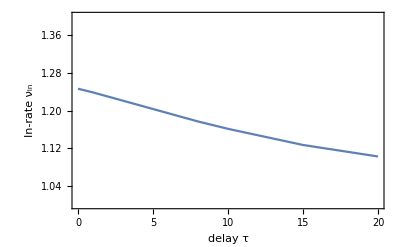

```mathematica
ListLinePlot[{#[[1]],If[#[[2,2]],#[[2,1]],∞]}&/@stabilityBoundaryAv,PlotRange->{{0,20},{1.0,1.4}},Frame->True,FrameLabel->{"delay τ","In-rate ν_in"}]
```

```mathematica
nuVals=Table[stabilityBoundaryAv[[n]][[2]][[1]], {n, 1,21,1}];
tauVals=Table[stabilityBoundaryAv[[n]][[1]], {n, 1,21,1}];
Export["stabBoundary_av_tauVals_N0_1.csv",tauVals];
Export["stabBoundary_av_nuVals_N0_1.csv", nuVals];
```